### I. Mathematical problems

```mathematica
1.
```

```mathematica
i)((x+1000)^4)^(1/4)=x+1000
```

```mathematica
f[x_]:=((x+1000)^4)^(1/4)
```

```mathematica
g[x_]:=x+1000
```

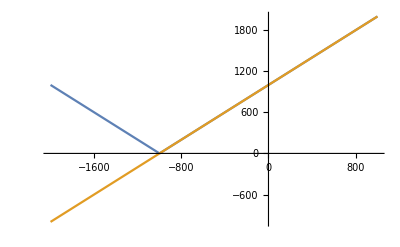

```mathematica
Plot[{f[x], g[x]},{x,-2000,1000}]
```

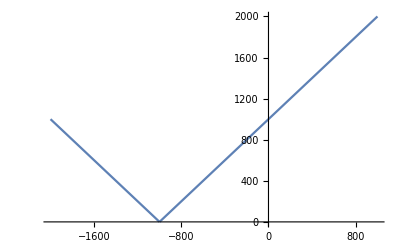

```mathematica
Plot[f[x], {x, -2000, 1000}]
```

```mathematica
f[1]
```

1001

```mathematica
g[1]
```

1001

```mathematica
f[-100]
```

900

```mathematica
g[-100]
```

900

```mathematica
f[1000000]
```

1001000

```mathematica
g[1000000]
```

1001000

```mathematica
f[-1001]
```

1

```mathematica
g[-1001]
```

-1

```mathematica
f[-10000000]
```

9999000

```mathematica
g[-10000000]
```

-9999000

```mathematica
The statement is true on the interval [-1000, ∞). 
This is so because as long as x + 1000 produces a positive output,
raising it to the 4th power and then taking the 4th root does not change the value.
However, once it becomes negative, raising it to the 4th power removes the negative, therefore altering the value.
```

```mathematica
ii).
```

```mathematica
h[x_]:=Sin[x]^5*Cos[x]^5
```

```mathematica
l[x_]:=(10Sin[2x]-5Sin[6x]+Sin[10x])/512
```

```mathematica
Simplify[l[x]]
```

Cos[x]^5 Sin[x]^5

The statement is true on the interval (-∞,∞), because when simplify is used, it becomes clear that the two functions are equivalent. They are the same function.

```mathematica
iii).
```

```mathematica
p[x_]:=ArcTan[x]+ArcTan[1/x]
```

```mathematica
n[x_]:=-π/2
```

```mathematica
N[p[-10000]]
```

-1.5708

```mathematica
N[n[-10000]]
```

-1.5708

```mathematica
N[p[10]]
```

1.5708

```mathematica
N[n[10]]
```

-1.5708

```mathematica
N[p[-5]]
```

-1.5708

```mathematica
N[n[-5]]
```

-1.5708

```mathematica
N[p[1000]]
```

1.5708

```mathematica
N[n[1000]]
```

-1.5708

```mathematica
N[p[0]]
```

Power::infy: Infinite expression 1/0 encountered.

Indeterminate

```mathematica
N[n[0]]
```

-1.5708

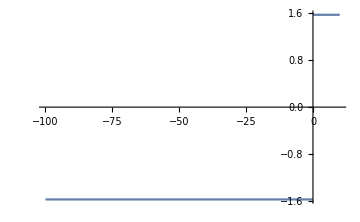

```mathematica
Plot[{p[x]},{x,-100,10}]
```

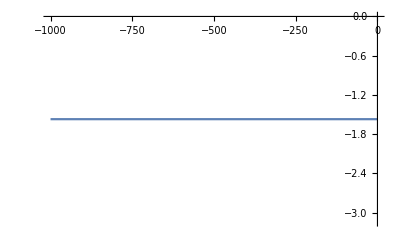

```mathematica
Plot[n[x],{x,-1000,0}]
```

The statement is true on the interval (-∞,0).

```mathematica
iv).
```

```mathematica
v[x_]:=ArcCos[x]
```

```mathematica
w[x_]:=-ⅈ*Log[x+√(x^2-1)]
```

```mathematica
v[1000.]
```

0.+7.6009 ⅈ

```mathematica
w[1000.]
```

0.-7.6009 ⅈ

```mathematica
v[-1000.]
```

3.14159-7.6009 ⅈ

```mathematica
w[-1000.]
```

3.14159+7.6009 ⅈ

```mathematica
v[0]
```

π/2

```mathematica
w[0]
```

π/2

```mathematica
v[3.]
```

0.+1.76275 ⅈ

```mathematica
w[3.]
```

0.-1.76275 ⅈ

```mathematica
v[153.]
```

0.+5.72357 ⅈ

```mathematica
w[153.]
```

0.-5.72357 ⅈ

```mathematica
Simplify[w[x]]
```

-ⅈ Log[x+√(-1+x^2)]

The real outputs of these two expressions are equivalent on the interval (-∞,∞). However, when imaginary components are included, the outputs are only the same on the interval [-1,1].

```mathematica
2.
```

```mathematica
i).
```

This sequence is created by doubling the previous term, using the formula t_n=t_(n-1)*2. Using this formula, the next three terms are 384, 768, 1536.

```mathematica
ii).
```

This sequence is created by subtracting 7 from the previous term, using the formula t_n=t_(n-1)-7. Using this formula, the next three terms are -34, -41, -48.

```mathematica
iii).
```

This sequence is created by adding one more than was added previously, using the formula t_n = t_(n-1) + n. Using this formula, the next three terms are 57, 68, 79.

```mathematica
iv).
```

This sequence is created by raising the index of the term to the third power, then multiplying it by 2, using the formula t_n=2 n^3. Using this formula, the next three terms are 1024, 1458, 2000.

```mathematica
v).
```

This sequence is created by multiplying the previous term by the index of the term being created, then subtracting the index of the previous term, using the formula t_n=t_(n-1)*n - (n-1). Using this formula, the next three terms are 362881, 3628801, 39916801.

```mathematica
3.
```

```mathematica
4.
```

```mathematica
Factor[x^(4^2)-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8)

```mathematica
Factor[x^(4^3)-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8) (1+x^16) (1+x^32)

```mathematica
Factor[x^(4^9)-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8) (1+x^16) (1+x^32) (1+x^64) (1+x^128) (1+x^256) (1+x^512) (1+x^1024) (1+x^2048) (1+x^4096) (1+x^8192) (1+x^16384) (1+x^32768) (1+x^65536) (1+x^131072)

```mathematica
Factor[x^(4^6)-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8) (1+x^16) (1+x^32) (1+x^64) (1+x^128) (1+x^256) (1+x^512) (1+x^1024) (1+x^2048)

```mathematica
Factor[x^(4^5)-1]
```

(-1+x) (1+x) (1+x^2) (1+x^4) (1+x^8) (1+x^16) (1+x^32) (1+x^64) (1+x^128) (1+x^256) (1+x^512)

The factorization is in the form of (x-1)∏_(i=0)^(2n-1) x^(2^i).

```mathematica
5.
```

```mathematica
k[x_]:=(Cos[x/7]+(Sin[x/15])^2)
```

```mathematica
FunctionPeriod[k[x],x]
```

210 π

The period is 210π. This was calculated by finding the periods of the two pieces of the functions, cos(x/7) and sin^2(x/15). The periods are 14π and 30π, respectively. To find the period of the combined function, the least common multiple of the two periods was calculated. This is 210π. To confirm, we used the FunctionPeriod built-in function.

```mathematica
6.
```

8000 miles * 5280 feet/mile = 42240000 feet. 300000 feet / 42240000 feet = 5/704. 5/704*10 inches = 25/352 inches.

```mathematica
7.
```

```mathematica
Abs[40-4 √103]
```

-40+4 √103

### II. Programming problems

```mathematica
1)
```

Our approach to this problem was to first create a helper function, squaredDigits, which uses the IntegerDigits function to create a list of the digits in the input number. Then, a for loop is used to go through each element in the list and square it, adding the squared result of each element to a result variable. This result is returned. In the main numberChain function, a while loop is used. This while loop calls the squaredDigits function until the result of squaredDigits is 1 or 89. The result of each iteration of squaredDigits is added to a string, which is returned.

```mathematica
numberChain[num_]:=Module[
(*local vars list *)
{squared = num,
numlist = ToString[num]},
(*while loop to continue until 1 or 89 is reached *)
While[
(* condition *)
squared≠89&&squared≠1,
(* body *)
squared = squaredDigits[squared];
numlist = numlist <>" " <>ToString[squared];
];
Return[numlist]
]
```

```mathematica
squaredDigits[num_]:=
(* creating list of digits in num using IntegerDigits function *)
(list=IntegerDigits[num];
(* result variable *)
res=0;
(*using for loop to square each digit in number *)
For[
(*start *)
i=1,
(* condition *) 
i ≤ Length[list],
(* update *)
i++, 
(* body *)
res+=list[[i]]^2
];
(*returning new number *)
Return[res];)
```

```mathematica
numberChain[1]
```

1

```mathematica
numberChain[10]
```

10 1

```mathematica
numberChain[2934923]
```

2934923 204 20 4 16 37 58 89

```mathematica
numberChain[2949]
```

2949 182 69 117 51 26 40 16 37 58 89

```mathematica
numberChain[15]
```

15 26 40 16 37 58 89

```mathematica
2)
```

```mathematica
t[number_]:= (number(number+1))/2
```

```mathematica
f[number_]:= (number(3number-1))/2
```

```mathematica
s[number_]:= number(2number-1)
```

a)

Our solution to this problem involves a series of for and while loops. First, we used 2 for loops to bring the iterations of each of our tracking variables to lower, the iteration at which the function is supposed to begin. Next, we used a while loop with the test of our 2 tracking variables not being equal to each other, the reasoning behind this being that once they are equal, we have found our number. Inside of this while loop, there is an if statement. This if statement determines which of our tracking variables has a lower value. The value of this variable is then increased using a while loop until it is greater than or, in the case of the common number being found, equal to the other tracking variable. As stated above, once they are equal, the outermost while loop will terminate, and the x, y, and the common number will be printed using a print statement.

```mathematica
triAndFif[lower_]:= Module[
(* initialize variables *)
{x = 1, 
y = 1, 
triTrack = 1, 
fifTrack = 1},
(*loops to bring tracker variable iterations to lower *)
For[(* start *)x, 
(* condition *)triTrack ≤lower, 
(* update *)x++, 
(* body *)triTrack =t[x];
];
For[(* start *)y, 
(* condition *)fifTrack ≤ lower, 
(* update *)y++,
(* body *)fifTrack = f[y];
];
(* while loops to determine which tracker is higher and adjust *)
While[(* test *)
triTrack ≠ fifTrack,
(* body - If statements determine which is higher *)
If[triTrack < fifTrack,
While[(* test *)
triTrack < fifTrack,
(*body - increasing triTrack *)
triTrack = t[x];
x++;
],
While[(* test *)
fifTrack < triTrack,
(* body - increasing fifTrack *)
fifTrack = f[y];
y++;
]
]
];
(* If statements for edge case of 1 *)
If[x == 1, x += 1];
If[y ==1, y += 1];
(* Print String *)
Print[ToString[x-1]<> " "<>ToString[y-1]<> " "<>ToString[triTrack]]
]
```

```mathematica
triAndFif[11]
```

20 12 210

```mathematica
triAndFif[210]
```

285 165 40755

```mathematica
triAndFif[1]
```

20 12 210

```mathematica
triAndFif[0]
```

1 1 1

```mathematica
triAndFif[293932]
```

3976 2296 7906276

```mathematica
b)
```

As this problem is very similar to the above problem, so is our solution. An additional for loop is added to bring the new sixTrack variable to the correct iteration. A new test has been added to the outermost While loop, accounting for the addition of the third variable, which needs to equal the other two. Additionally, inside of this While loop, 2 an additional If statements, containing while loops, are used to bring the value of the new sixTrack variable to be greater than or equal to the value of the other variables. When all of the variables are equivalent, the outermost While loop terminates. The x, y, and z values, along with the common number, are then printed using a Print statement.

```mathematica
Clear[x,y,triTrack,fifTrack]
```

```mathematica
triAndFifAndSix[lower_]:= Module[
(* Declare local variables *)
{x = 1,
y = 1,
z = 1, 
triTrack = 1, 
fifTrack = 1, 
sixTrack = 1},
(* loops to bring tracker variable iterations to lower *)
For[(* start *)x, 
(* condition *)triTrack ≤lower, 
(* update *)x++, 
(* body *)triTrack =t[x];
];
For[(* start *)y, 
(*condition *)fifTrack ≤ lower, 
(* update *)y++,
(* body *)fifTrack = f[y];
];
For[(* start *)z, 
(* condition *)sixTrack ≤ lower, 
(* update *)z++,
(* body *)sixTrack = s[z];
];
(* while loops to determine which tracker is highest and adjust *)
While[(* test *)triTrack ≠ fifTrack ||triTrack ≠ sixTrack,
(* body - If statements determining which is highest *)
If[triTrack < fifTrack,
While[(* test *)triTrack < fifTrack,
(*body - increasing triTrack *)
triTrack = t[x];
x++;
]
];
If[triTrack < sixTrack,
While[(* test *)triTrack < sixTrack,
(*body - increasing triTrack *)
triTrack = t[x];
x++;
]
];
If[fifTrack < triTrack,
While[(* test *)fifTrack < triTrack,
(*body - increasing fifTrack *)
fifTrack = f[y];
y++;
]
];
If[sixTrack < triTrack,
While[(* test *)sixTrack  < triTrack,
(*body - increasing sixTrack *)
sixTrack = s[z];
z++;
]
]
];
(* If statements for edge case of 1 *)
If[x == 1, x += 1];
If[y ==1, y += 1];
If[z == 1, z += 1];
(* Printing String *)
Print[ToString[x-1]<> " "<>ToString[y-1]<> " "<>ToString[z -1]<>" " <>ToString[triTrack]]
]
```

```mathematica
triAndFifAndSix[210]
```

285 165 143 40755

```mathematica
triAndFifAndSix[0]
```

1 1 1 1

```mathematica
triAndFifAndSix[1]
```

285 165 143 40755

```mathematica
triAndFifAndSix[40755]
```

55385 31977 27693 1533776805

```mathematica
triAndFifAndSix[299394]
```

55385 31977 27693 1533776805